## GenerateBoundaryLayer-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 17:32:16
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

Generate 50 random vertices to use a Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
v=Table[{r,r}, {50}];
```

```mathematica
v
```

{{6.54796,84.7634},{15.7378,50.4957},{5.43344,62.9925},{24.3956,89.3217},{18.394,62.2654},{98.3388,46.9323},{27.6807,82.8499},{9.46174,44.1906},{63.6563,25.4924},{70.9656,4.82385},{5.39048,32.0473},{83.7593,85.7743},{92.6678,36.2433},{78.1741,0.302939},{62.093,94.3811},{73.845,8.28576},{86.9846,16.0963},{55.9238,8.62038},{3.18989,88.0023},{81.8415,95.2611},{61.247,29.823},{44.6866,48.7742},{42.0287,12.1632},{88.1837,71.7192},{93.5855,62.9952},{96.7169,6.87673},{98.5319,46.2005},{66.9146,61.014},{56.5227,47.6885},{59.0427,70.9538},{36.4352,14.2665},{66.5852,4.19954},{36.3054,71.0011},{15.1678,66.2985},{30.3414,83.121},{72.4964,22.3784},{22.3565,23.6098},{46.1723,86.7727},{66.8769,8.82738},{45.0292,93.0792},{49.6378,43.3638},{38.5213,41.4833},{80.4153,58.8937},{83.9317,45.239},{57.6992,78.9244},{86.2314,62.5471},{58.5867,98.2576},{32.9826,64.3182},{25.2119,19.6735},{89.6875,87.5218}}

```mathematica
bl=GenerateBoundaryLayer[v]
```

{{-10.2338,38.3254},{-9.91808,23.1595},{-1.09148,16.6849},{7.81669,10.3799},{16.6708,4.16881},{29.4717,-2.00789},{36.1528,-4.5347},{50.2265,-8.78556},{64.3732,-13.121},{78.3833,-17.3974},{89.0709,-12.679},{99.955,-8.3982},{110.935,-3.66775},{112.384,9.03809},{113.531,21.8402},{114.977,34.6796},{116.173,47.6569},{113.347,59.7403},{110.563,71.9859},{107.802,83.9418},{105.209,96.0325},{97.5068,103.434},{89.5945,111.175},{79.2121,112.685},{68.7635,114.261},{58.1008,115.952},{44.5014,112.411},{30.5544,109.039},{16.7658,105.732},{2.96014,102.414},{-10.6385,99.0531},{-10.3451,83.8886},{-10.4209,68.7932},{-10.1747,53.5123}}

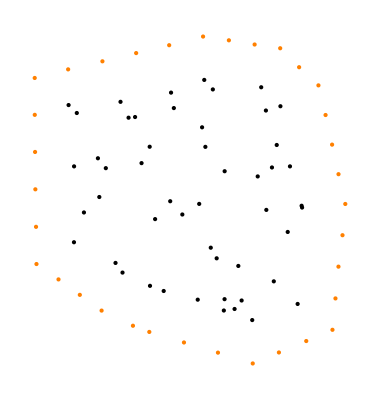

```mathematica
Graphics[{Point[v], Orange, Point[bl]}]
```

Use the Voronoi Centers to generate a tissue with 50 cells using the Bounded-Cell-Voronoi algorithm

```mathematica
w=BoundedCellVoronoi[v];
```

Show the tissue, original Voronoi Centers, and artificial Boundary Layer centers.

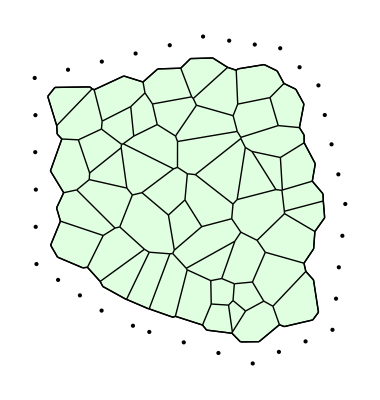

```mathematica
Show[ShowTissue[w], 
Graphics[Point[bl]]]
```

```mathematica
bcv=BoundedCellVoronoi[Join[v,bl]];
```

```mathematica
COB = CellsOnBoundary[bcv]
```

{51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84}

```mathematica
cc=If[MemberQ[COB,#], LightBlue, Pink]&/@Range[NTissueCells[bcv]];
```

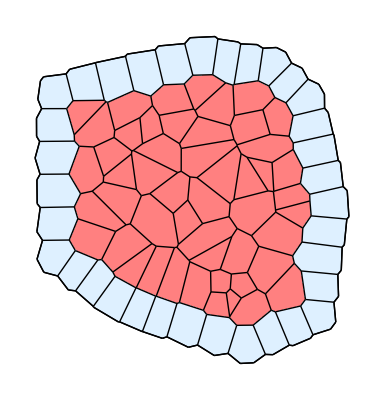

```mathematica
ShowTissue[bcv, "CellStyles"-> cc]
```